```mathematica
SetDirectory[NotebookDirectory[]];
data = SetPrecision[Import["particles.out","Table"],8];
(*When we read the table, we convert each entry to string, remove the commas, and then convert back to expression. The level {2} indicates that we use this function on the second level. *)
data =Map[ToExpression[StringReplace[ToString[#],","->""]]&,data,{2}];
inputs =Flatten[ Import["inputs.in", "Table"]];
partRadii=Flatten[Import["part_radii.out", "Table"]];

numPart = inputs⟦2⟧;
boxSize =inputs⟦5⟧;
dt=inputs⟦4⟧;
shearRate=inputs⟦6⟧;
endTime=data⟦2⟧⟦1⟧;

Wrap[x_]:=Mod[x+boxSize/2,boxSize]-boxSize/2;
shearMove=Wrap[shearRate*boxSize/2*dt*endTime];
Print["The top row is shifted by ", shearMove];
(*Used to tile the duplicate spheres. *)
duplicateDir={{0,1,0},{0,-1,0},{1,0,0},{-1,0,0},{1,1,0},{1,-1,0},{-1,1,0},{-1,-1,0}};
(*Grab the y-coord to determine how much x to shift for the shear. *)
shiftDir=Map[#⟦2⟧&,duplicateDir];

(*Create a table with the "Sphere" graphics objects*)
(*Centre positions are stored from the 2nd row onwards*)
graphicsset =Table[
Sphere[data⟦i+1⟧⟦3;;5⟧,partRadii⟦i⟧],
{i,1,numPart}
];
(*Sphere positions for the tiled spheres. Each "group" of tiled sphere has a different colour. *)
dupe=Table[
{Hue[j/Length[duplicateDir]],Sphere[data⟦i+1⟧⟦3;;5⟧+boxSize*duplicateDir⟦j⟧+shearMove*{1,0,0}*shiftDir⟦j⟧,partRadii⟦i⟧]},
{i,1,numPart},{j,1,Length[duplicateDir]}
];
(*Combine the original spheres with the tiles. *)
graphicsset=Union[graphicsset,dupe];
(*Find the dimensions of the enclosing box*)
{xmin,ymin,zmin}={-boxSize/2,-boxSize/2,-boxSize/2};
{xmax,ymax,zmax}={boxSize/2,boxSize/2,boxSize/2};
volume = boxSize^3;
occupied =Sum[ 4/3*π*partRadii⟦i⟧^3,{i,1,numPart}];

packfraction = N[occupied/volume];
Print["We have ", numPart," particles."]
Print["Their radii are ",partRadii]
Print["Occupied volume is ", occupied, " out of ", volume, ", the packing fraction is ",packfraction]
(* For 3D packing! *)
Graphics3D[graphicsset, Axes->True,AxesLabel->{x,y,z},ViewPoint->{0,0,2}]
```

The top row is shifted by 0.

We have 50 particles.

Their radii are {2.18087,1.99347,2.7982,2.77483,1.39285,3.11809,2.069,3.67216,1.63293,2.30171,2.78096,2.18513,2.0644,4.26828,3.02309,3.24504,3.39766,4.25241,4.39074,2.39089,3.31871,2.34336,3.64504,3.93066,2.23782,1.02909,4.89612,3.31099,0.591062,3.07795,1.17715,2.13286,1.8881,2.35028,3.13958,3.41032,1.51835,2.19694,2.1569,3.59837,0.464448,1.46045,1.85961,2.88506,3.13707,2.26976,3.13247,2.90008,2.97017,1.37113}

Occupied volume is 5238.8 out of 3375, the packing fraction is 1.55224

-Graphics3D-

```mathematica
(* This file contains the relative vectors from particle i to j in rows. It first has the vectors from i to all other j, and iterates over i. *)
(* Take the norm of the relative vector, stored in entries 3 to 5. *)
(* Initially it's in one long list so we reshape into a square matrix. *)
vecData= Import["part_vec.out"];
normData=Map[Norm[#⟦3;;5⟧]&,vecData];
normData=ArrayReshape[normData,{numPart,numPart}];
```

{11,5,11,9,4,10,8,13,6,8,10,8,7,18,11,11,16,17,23,7,15,8,16,15,11,4,22,12,3,15,4,8,7,10,12,14,6,10,10,15,1,4,6,11,12,8,16,12,11,5}

10.32

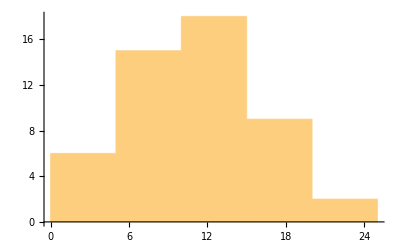

```mathematica
(*For each pair of particles check if their distance is less than the sum of their radii. This means that they are touching and thus we count as True. *)
TouchingTable = Table[
normData⟦i⟧⟦j⟧<(partRadii⟦i⟧+partRadii⟦j⟧),
{i,1,numPart},
{j,1,numPart}
];
(*Count how many True (touching spheres) there are per particle, and minus 1 to ignore itself. *)
TouchingSpheres=Map[Count[#,True]&,TouchingTable]-1
N[Mean[TouchingSpheres]]
Histogram[TouchingSpheres]
```

```mathematica
(*For a given set, scale the values from 0 to 0.7 to be fed into Hue[] function. *)
NormColour[set_]:=(set-Min[set])/(Max[set]-Min[set])*7/10;
TouchingNumColour=NormColour[TouchingSpheres];
(*Draw the main cell with colours based on coordination number. Small is red, large is blue. *)
graphicsset2=Table[
{Hue[TouchingNumColour⟦i⟧],Sphere[data⟦i+1⟧⟦3;;5⟧,partRadii⟦i⟧]},
{i,1,numPart}
];
Graphics3D[graphicsset2, Axes->True,AxesLabel->{x,y,z},ViewPoint->{0,0,2}]
```

-Graphics3D-

```mathematica
(*meancoord = Table[
TouchingSpheres=(Count[DistanceBtwCentres_/;DistanceBtwCentres<limit*d]/@DistTable)-1;
N[Mean[TouchingSpheres]],
{limit,{1.000001,1.0001,1.001,1.002,1.004,1.006,1.008,1.01,1.02,1.03,1.04,1.05,1.06,1.07,1.08,1.09,1.1}}]*)
(*limitlist={1.000001,1.0001,1.001,1.002,1.004,1.006,1.008,1.01,1.02,1.03,1.04,1.05,1.06,1.07,1.08,1.09,1.1};
ListPlot[Transpose[{limitlist,meancoord}]]*)
```